```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->-t]
```

```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.001,1,0]],B:=Inverse[β[ω,0.001,1,0]],T1:=T1[1]},Do[J=Inverse[IdentityMatrix[14]-B.ConjugateTranspose[T1].J.T1].B,3000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]
```

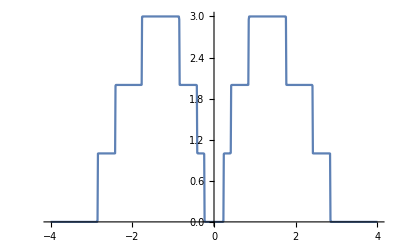

```mathematica
ListLinePlot[Table[{ω,Abs[tr[ω,0.0001,1,0]]},{ω,Range[-4,4,0.01]}]]
```

```mathematica
Export["Leads7agnr.dat",Table[{ω,LEFT[ω,0.0001,1,0]},{ω,Range[0,4,0.01]}]]
```

Leads7agnr.dat

```mathematica
tr[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{},A:=Module[{gg=g[ω,δ,t,ϵ],P=T1[1]},
sl1=Module[{J=SL[ω,δ,t,ϵ]},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,7}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{8,14}]},ReplacePart[κ,{{μ1,μ1},(*{μ2,μ2},*){μ3,μ3}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[P].J.P].c],1];J=J];sl2= Module[{J=sl1},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,7}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{8,14}]},ReplacePart[κ,{{μ1,μ1},(*{μ2,μ2},*){μ3,μ3}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[P].J.P].c],1];J=J];sl3= Module[{J=sl2},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,5}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{11,14}]},ReplacePart[κ,{{μ1,μ1},{μ2,μ2},{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[P].J.P].c],1];J=J];sl4= Module[{J=sl3},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,5}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{11,14}]},ReplacePart[κ,{{μ1,μ1},{μ2,μ2},{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[P].J.P].c],1];J=J];Il1:=Inverse[IdentityMatrix[14]-sl4.TT[1].SR[ω,δ,1,0].TT[1]].sl4;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,δ,1,0].TT[1].sl4.TT[1]].SR[ω,δ,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,δ,1,0].TT[1].Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.TT[1].grr1.TT[1]-TT[1].GNON1.TT[1].GNON1]]];B:=Module[{},η=Module[{gg=g[ω,δ,t,ϵ],P=T1[1]},
sl1= Module[{J=SL[ω,δ,t,ϵ]},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,5}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{11,14}]},ReplacePart[κ,{{μ1,μ1},{μ2,μ2},{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[P].J.P].c],1];J=J];sl2= Module[{J=sl1},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,7}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{8,14}]},ReplacePart[κ,{{μ1,μ1},(*{μ2,μ2},*){μ3,μ3}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[P].J.P].c],1];J=J];sl3= Module[{J=sl2},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,7}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{8,14}]},ReplacePart[κ,{{μ1,μ1},(*{μ2,μ2},*){μ3,μ3}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[P].J.P].c],1];J=J];sl4= Module[{J=sl3},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,5}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{11,14}]},ReplacePart[κ,{{μ1,μ1},{μ2,μ2},{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[P].J.P].c],1];J=J];Il1:=Inverse[IdentityMatrix[14]-sl4.TT[1].SR[ω,δ,1,0].TT[1]].sl4;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,δ,1,0].TT[1].sl4.TT[1]].SR[ω,δ,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,δ,1,0].TT[1].Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.TT[1].grr1.TT[1]-TT[1].GNON1.TT[1].GNON1]]];η];Y:=Module[{},η=Module[{gg=g[ω,δ,t,ϵ],P=T1[1]},
sl1= Module[{J=SL[ω,δ,t,ϵ]},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,7}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{8,14}]},ReplacePart[κ,{{μ1,μ1},(*{μ2,μ2},*){μ3,μ3}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[P].J.P].c],1];J=J];sl2= Module[{J=sl1},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,5}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{11,14}]},ReplacePart[κ,{{μ1,μ1},{μ2,μ2},{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[P].J.P].c],1];J=J];sl3= Module[{J=sl2},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,7}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{8,14}]},ReplacePart[κ,{{μ1,μ1},(*{μ2,μ2},*){μ3,μ3}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[P].J.P].c],1];J=J];sl4= Module[{J=sl3},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,5}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{11,14}]},ReplacePart[κ,{{μ1,μ1},{μ2,μ2},{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[P].J.P].c],1];J=J];Il1:=Inverse[IdentityMatrix[14]-sl4.TT[1].SR[ω,δ,1,0].TT[1]].sl4;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,δ,1,0].TT[1].sl4.TT[1]].SR[ω,δ,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,δ,1,0].TT[1].Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.TT[1].grr1.TT[1]-TT[1].GNON1.TT[1].GNON1]]];η];R:=Module[{},η=Module[{gg=g[ω,δ,t,ϵ],P=T1[1]},
sl1= Module[{J=SL[ω,δ,t,ϵ]},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,5}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{11,14}]},ReplacePart[κ,{{μ1,μ1},{μ2,μ2},{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[P].J.P].c],1];J=J];sl2= Module[{J=sl1},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,14}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{11,14}]},ReplacePart[κ,{{μ1,μ1}(*,{μ2,μ2},{μ3,μ3}*)}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[P].J.P].c],1];J=J];sl3= Module[{J=sl2},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,5}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{11,14}]},ReplacePart[κ,{{μ1,μ1},{μ2,μ2},{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[P].J.P].c],1];J=J];sl4= Module[{J=sl3},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,5}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{11,14}]},ReplacePart[κ,{{μ1,μ1},{μ2,μ2},{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[P].J.P].c],1];J=J];Il1:=Inverse[IdentityMatrix[14]-sl4.TT[1].SR[ω,δ,1,0].TT[1]].sl4;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,δ,1,0].TT[1].sl4.TT[1]].SR[ω,δ,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,δ,1,0].TT[1].Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.TT[1].grr1.TT[1]-TT[1].GNON1.TT[1].GNON1]]];η];P:=Module[{},η=Module[{gg=g[ω,δ,t,ϵ],P=T1[1]},
sl1= Module[{J=SL[ω,δ,t,ϵ]},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,5}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{11,14}]},ReplacePart[κ,{{μ1,μ1},{μ2,μ2},{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[P].J.P].c],1];J=J];sl2= Module[{J=sl1},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,5}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{11,14}]},ReplacePart[κ,{{μ1,μ1},{μ2,μ2},{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[P].J.P].c],1];J=J];sl3= Module[{J=sl2},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,5}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{11,14}]},ReplacePart[κ,{{μ1,μ1},{μ2,μ2},{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[P].J.P].c],1];J=J];sl4= Module[{J=sl3},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,14}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{11,14}]},ReplacePart[κ,{{μ1,μ1}(*,{μ2,μ2},{μ3,μ3}*)}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[P].J.P].c],1];J=J];Il1:=Inverse[IdentityMatrix[14]-sl4.TT[1].SR[ω,δ,1,0].TT[1]].sl4;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,δ,1,0].TT[1].sl4.TT[1]].SR[ω,δ,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,δ,1,0].TT[1].Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.TT[1].grr1.TT[1]-TT[1].GNON1.TT[1].GNON1]]];η];(A+B+Y+R+P)/5]
```

```mathematica
tr[0,0.001,1,0,1]
```

0.0133259

```mathematica
Mean[Table[tr[0.13,0.001,1,0,1],4000]]
```

0.00664

```mathematica
Export["10imp7.csv",Table[{ω,Mean[Table[tr[ω,0.001,1,0,0.7],2000]]},{ω,Range[0,4,0.01]}]]
```

10imp7.csv

```mathematica
Export["10imp5.csv",Table[{ω,Mean[Table[tr[ω,0.001,1,0,0.5],2000]]},{ω,Range[0,4,0.01]}]]
```

10imp5.csv

```mathematica
Export["10imp3.csv",Table[{ω,Mean[Table[tr[ω,0.001,1,0,0.3],2000]]},{ω,Range[0,4,0.01]}]]
```

10imp3.csv

```mathematica
Export["10imp9.csv",Table[{ω,Mean[Table[tr[ω,0.001,1,0,0.9],2000]]},{ω,Range[0,4,0.01]}]]
```

10imp9.csv

```mathematica
tr1[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{},η=Module[{gg=g[ω,δ,t,ϵ],P=T1[1]},
sl1= Module[{J=SL[ω,δ,t,ϵ]},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,5}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{11,14}]},ReplacePart[κ,{{μ1,μ1},{μ2,μ2},{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[P].J.P].c],4];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.TT[1].SR[ω,δ,1,0].TT[1]].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,δ,1,0].TT[1].sl1.TT[1]].SR[ω,δ,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,δ,1,0].TT[1].Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.TT[1].grr1.TT[1]-TT[1].GNON1.TT[1].GNON1]]];η]
```

```mathematica
Mean[Table[tr1[1.2,0.001,1,0,0.7],2000]]
```

0.99575

```mathematica
Export["12imp7.csv",Table[{ω,Mean[Table[tr1[ω,0.001,1,0,0.7],2000]]},{ω,Range[0,4,0.01]}]]
```

12imp7.csv

```mathematica
Export["12imp5.csv",Table[{ω,Mean[Table[tr1[ω,0.001,1,0,0.5],2000]]},{ω,Range[0,4,0.01]}]]
```

12imp5.csv

```mathematica
Export["12imp3.csv",Table[{ω,Mean[Table[tr1[ω,0.001,1,0,0.3],2000]]},{ω,Range[0,4,0.01]}]]
```

12imp3.csv

```mathematica
Import["12imp3.csv"]
```

{{0.,0.000196014},{0.01,0.000141934},{0.02,0.000100738},{0.03,0.0000733334},{0.04,0.0000573291},{0.05,0.000046631},{0.06,0.000038992},{0.07,0.0000491537},{0.08,0.0000667508},{0.09,0.0000954161},{0.1,0.000129468},{0.11,0.000187436},{0.12,0.000256688},{0.13,0.000351478},{0.14,0.000488451},{0.15,0.00065649},{0.16,0.00084755},{0.17,0.00107868},{0.18,0.00141022},{0.19,0.00205004},{0.2,0.00278206},{0.21,0.00395971},{0.22,0.00591344},{0.23,0.0102173},{0.24,0.065638},{0.25,0.195226},{0.26,0.314494},{0.27,0.417259},{0.28,0.507753},{0.29,0.588586},{0.3,0.661044},{0.31,0.716358},{0.32,0.76769},{0.33,0.800277},{0.34,0.827161},{0.35,0.850301},{0.36,0.866116},{0.37,0.876728},{0.38,0.88214},{0.39,0.877894},{0.4,0.860511},{0.41,0.823577},{0.42,0.83035},{0.43,0.984935},{0.44,1.12049},{0.45,1.22253},{0.46,1.31689},{0.47,1.38324},{0.48,1.46516},{0.49,1.52366},{0.5,1.5765},{0.51,1.62098},{0.52,1.66177},{0.53,1.68708},{0.54,1.72553},{0.55,1.748},{0.56,1.76542},{0.57,1.78477},{0.58,1.79837},{0.59,1.81416},{0.6,1.82705},{0.61,1.83116},{0.62,1.84125},{0.63,1.85147},{0.64,1.85543},{0.65,1.85802},{0.66,1.85905},{0.67,1.86042},{0.68,1.86525},{0.69,1.86708},{0.7,1.8662},{0.71,1.86568},{0.72,1.86645},{0.73,1.86765},{0.74,1.86432},{0.75,1.86542},{0.76,1.86295},{0.77,1.86087},{0.78,1.85769},{0.79,1.85581},{0.8,1.84999},{0.81,1.84134},{0.82,1.8298},{0.83,1.80829},{0.84,1.77412},{0.85,1.65278},{0.86,1.76666},{0.87,1.85878},{0.88,1.95723},{0.89,2.05085},{0.9,2.14321},{0.91,2.22938},{0.92,2.30371},{0.93,2.37979},{0.94,2.44258},{0.95,2.49462},{0.96,2.54504},{0.97,2.59217},{0.98,2.63014},{0.99,2.66179},{1.,2.68141},{1.01,2.69411},{1.02,2.66967},{1.03,2.45763},{1.04,1.96817},{1.05,2.30371},{1.06,2.26183},{1.07,1.95156},{1.08,1.73027},{1.09,2.09467},{1.1,2.1884},{1.11,2.12068},{1.12,2.19889},{1.13,2.37359},{1.14,2.50048},{1.15,2.55451},{1.16,2.59591},{1.17,2.62247},{1.18,2.63946},{1.19,2.64514},{1.2,2.65445},{1.21,2.65927},{1.22,2.66455},{1.23,2.67136},{1.24,2.67226},{1.25,2.67519},{1.26,2.67358},{1.27,2.67645},{1.28,2.67904},{1.29,2.68394},{1.3,2.68555},{1.31,2.68414},{1.32,2.69071},{1.33,2.68451},{1.34,2.68736},{1.35,2.6815},{1.36,2.68043},{1.37,2.68179},{1.38,2.68187},{1.39,2.67962},{1.4,2.67291},{1.41,2.6707},{1.42,2.66765},{1.43,2.66597},{1.44,2.65992},{1.45,2.6602},{1.46,2.6548},{1.47,2.65286},{1.48,2.64742},{1.49,2.64646},{1.5,2.64491},{1.51,2.63551},{1.52,2.63278},{1.53,2.63672},{1.54,2.62139},{1.55,2.61967},{1.56,2.60391},{1.57,2.5941},{1.58,2.58412},{1.59,2.58303},{1.6,2.56531},{1.61,2.55708},{1.62,2.53831},{1.63,2.52231},{1.64,2.50837},{1.65,2.49615},{1.66,2.47219},{1.67,2.45875},{1.68,2.44196},{1.69,2.42065},{1.7,2.38068},{1.71,2.34413},{1.72,2.26315},{1.73,2.17119},{1.74,2.03787},{1.75,1.86645},{1.76,1.47095},{1.77,2.28794},{1.78,3.39717},{1.79,2.30342},{1.8,1.437},{1.81,1.37728},{1.82,1.42953},{1.83,1.41816},{1.84,1.4257},{1.85,1.58097},{1.86,1.71116},{1.87,1.78175},{1.88,1.80727},{1.89,1.82438},{1.9,1.83578},{1.91,1.84262},{1.92,1.84712},{1.93,1.85185},{1.94,1.85261},{1.95,1.85124},{1.96,1.85538},{1.97,1.85728},{1.98,1.85662},{1.99,1.85738},{2.,1.85785},{2.01,1.85884},{2.02,1.8588},{2.03,1.85937},{2.04,1.85917},{2.05,1.86285},{2.06,1.86264},{2.07,1.86252},{2.08,1.85924},{2.09,1.86071},{2.1,1.86038},{2.11,1.85681},{2.12,1.85503},{2.13,1.85584},{2.14,1.85216},{2.15,1.84948},{2.16,1.84394},{2.17,1.84119},{2.18,1.83612},{2.19,1.83119},{2.2,1.82934},{2.21,1.82306},{2.22,1.82012},{2.23,1.81406},{2.24,1.81448},{2.25,1.8138},{2.26,1.8117},{2.27,1.80732},{2.28,1.8095},{2.29,1.80823},{2.3,1.80229},{2.31,1.79648},{2.32,1.78186},{2.33,1.76395},{2.34,1.74491},{2.35,1.71407},{2.36,1.66686},{2.37,1.6209},{2.38,1.55984},{2.39,1.4747},{2.4,1.36281},{2.41,1.0959},{2.42,1.9564},{2.43,1.34709},{2.44,0.795564},{2.45,0.832486},{2.46,0.950727},{2.47,0.977935},{2.48,0.838458},{2.49,0.861661},{2.5,0.893896},{2.51,0.925711},{2.52,0.93831},{2.53,0.943515},{2.54,0.947207},{2.55,0.949098},{2.56,0.947752},{2.57,0.946932},{2.58,0.945793},{2.59,0.943319},{2.6,0.940752},{2.61,0.941638},{2.62,0.937106},{2.63,0.938154},{2.64,0.936588},{2.65,0.938643},{2.66,0.940479},{2.67,0.940225},{2.68,0.943763},{2.69,0.945485},{2.7,0.945031},{2.71,0.948207},{2.72,0.947501},{2.73,0.944194},{2.74,0.940064},{2.75,0.93271},{2.76,0.914838},{2.77,0.893216},{2.78,0.861251},{2.79,0.822848},{2.8,0.780597},{2.81,0.730497},{2.82,0.676459},{2.83,0.611596},{2.84,0.503169},{2.85,0.394304},{2.86,0.360966},{2.87,0.0358584},{2.88,0.0204897},{2.89,0.0598545},{2.9,0.082018},{2.91,0.0553633},{2.92,0.0155543},{2.93,0.00494069},{2.94,0.00274634},{2.95,0.00190208},{2.96,0.0014883},{2.97,0.00111502},{2.98,0.000943123},{2.99,0.000750672},{3.,0.000650837},{3.01,0.000536337},{3.02,0.000436632},{3.03,0.000405935},{3.04,0.000344583},{3.05,0.00030095},{3.06,0.000260803},{3.07,0.00023677},{3.08,0.000203043},{3.09,0.000184818},{3.1,0.000159429},{3.11,0.000145429},{3.12,0.000126576},{3.13,0.000120829},{3.14,0.000104162},{3.15,0.000100791},{3.16,0.0000895385},{3.17,0.0000852492},{3.18,0.0000737082},{3.19,0.0000671884},{3.2,0.0000620894},{3.21,0.0000568696},{3.22,0.0000527666},{3.23,0.0000489631},{3.24,0.0000442454},{3.25,0.0000398321},{3.26,0.0000408536},{3.27,0.0000359829},{3.28,0.0000324213},{3.29,0.000030026},{3.3,0.0000289777},{3.31,0.0000266576},{3.32,0.0000249305},{3.33,0.0000240366},{3.34,0.0000222018},{3.35,0.0000199118},{3.36,0.0000186368},{3.37,0.0000176732},{3.38,0.0000164673},{3.39,0.0000158346},{3.4,0.0000146446},{3.41,0.0000136733},{3.42,0.0000134127},{3.43,0.0000126679},{3.44,0.0000119482},{3.45,0.0000109824},{3.46,9.88095×10^-6},{3.47,9.74018×10^-6},{3.48,8.94256×10^-6},{3.49,8.75096×10^-6},{3.5,7.94428×10^-6},{3.51,7.94615×10^-6},{3.52,7.33436×10^-6},{3.53,7.08424×10^-6},{3.54,6.99865×10^-6},{3.55,6.46199×10^-6},{3.56,5.80816×10^-6},{3.57,5.56338×10^-6},{3.58,5.53131×10^-6},{3.59,5.19708×10^-6},{3.6,5.02544×10^-6},{3.61,4.676×10^-6},{3.62,4.42966×10^-6},{3.63,4.21101×10^-6},{3.64,4.11173×10^-6},{3.65,3.78664×10^-6},{3.66,3.53942×10^-6},{3.67,3.5835×10^-6},{3.68,3.30127×10^-6},{3.69,3.20658×10^-6},{3.7,3.03099×10^-6},{3.71,3.03207×10^-6},{3.72,2.83219×10^-6},{3.73,2.66801×10^-6},{3.74,2.51121×10^-6},{3.75,2.3975×10^-6},{3.76,2.30429×10^-6},{3.77,2.22974×10^-6},{3.78,2.18239×10^-6},{3.79,1.99967×10^-6},{3.8,1.90259×10^-6},{3.81,1.91366×10^-6},{3.82,1.78035×10^-6},{3.83,1.69645×10^-6},{3.84,1.65151×10^-6},{3.85,1.57386×10^-6},{3.86,1.50307×10^-6},{3.87,1.4197×10^-6},{3.88,1.36129×10^-6},{3.89,1.38997×10^-6},{3.9,1.30558×10^-6},{3.91,1.25715×10^-6},{3.92,1.21581×10^-6},{3.93,1.14464×10^-6},{3.94,1.10958×10^-6},{3.95,1.0265×10^-6},{3.96,9.99678×10^-7},{3.97,9.8636×10^-7},{3.98,9.12003×10^-7},{3.99,9.20359×10^-7},{4.,8.50333×10^-7}}

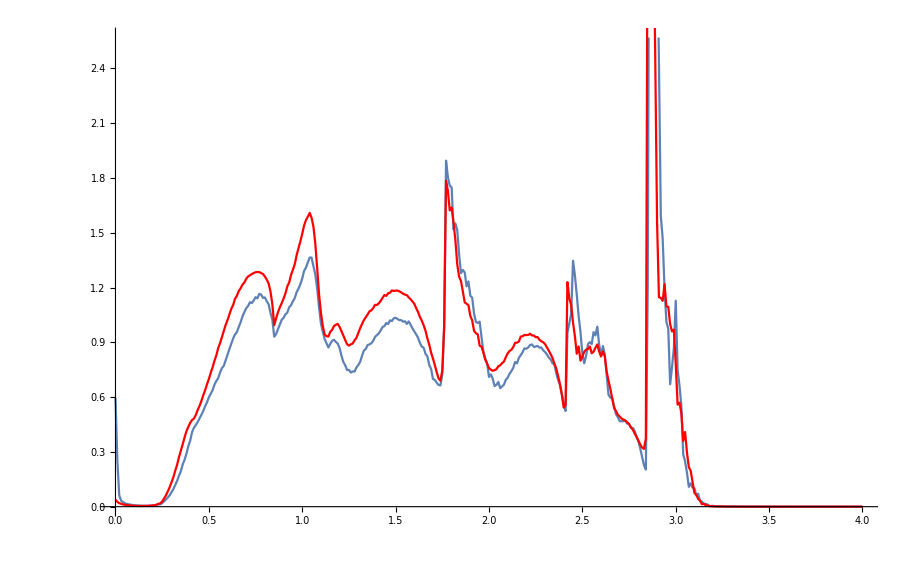

```mathematica
Show[ListPlot[Import["12imp9.csv"],Joined->True],ListPlot[Import["10imp9.csv"],Joined->True,PlotStyle->Red]]
```

```mathematica
Export["12imp9.csv",Table[{ω,Mean[Table[tr1[ω,0.001,1,0,0.9],2000]]},{ω,Range[0,4,0.01]}]]
```

12imp9.csv

```mathematica
Import["12imp9.csv"]
```

{{0.,0.596654},{0.01,0.253889},{0.02,0.0630595},{0.03,0.0336148},{0.04,0.0252833},{0.05,0.0189165},{0.06,0.0156585},{0.07,0.0132599},{0.08,0.0110984},{0.09,0.00933863},{0.1,0.00783273},{0.11,0.00704333},{0.12,0.00666827},{0.13,0.00586959},{0.14,0.00535537},{0.15,0.00515398},{0.16,0.0051703},{0.17,0.00498671},{0.18,0.00525105},{0.19,0.00573406},{0.2,0.00652489},{0.21,0.00750633},{0.22,0.00918964},{0.23,0.0123348},{0.24,0.0129298},{0.25,0.0197402},{0.26,0.0286392},{0.27,0.0391488},{0.28,0.0494644},{0.29,0.0627174},{0.3,0.0790401},{0.31,0.0968518},{0.32,0.118891},{0.33,0.141442},{0.34,0.169925},{0.35,0.19347},{0.36,0.231754},{0.37,0.256766},{0.38,0.290299},{0.39,0.331604},{0.4,0.361629},{0.41,0.408093},{0.42,0.432131},{0.43,0.446685},{0.44,0.463671},{0.45,0.483418},{0.46,0.503115},{0.47,0.52414},{0.48,0.550356},{0.49,0.571133},{0.5,0.598439},{0.51,0.618969},{0.52,0.637975},{0.53,0.668081},{0.54,0.688963},{0.55,0.703747},{0.56,0.734599},{0.57,0.759266},{0.58,0.771409},{0.59,0.80263},{0.6,0.83265},{0.61,0.862843},{0.62,0.892595},{0.63,0.921088},{0.64,0.942893},{0.65,0.956022},{0.66,0.984176},{0.67,1.00976},{0.68,1.04207},{0.69,1.06527},{0.7,1.08671},{0.71,1.0992},{0.72,1.11987},{0.73,1.1151},{0.74,1.12942},{0.75,1.14737},{0.76,1.14113},{0.77,1.16559},{0.78,1.16146},{0.79,1.14343},{0.8,1.14605},{0.81,1.12511},{0.82,1.10834},{0.83,1.0619},{0.84,1.02499},{0.85,0.930885},{0.86,0.945224},{0.87,0.972357},{0.88,0.997367},{0.89,1.02378},{0.9,1.0339},{0.91,1.05317},{0.92,1.06256},{0.93,1.09181},{0.94,1.10312},{0.95,1.12466},{0.96,1.14255},{0.97,1.17504},{0.98,1.19387},{0.99,1.21837},{1.,1.24964},{1.01,1.29149},{1.02,1.30949},{1.03,1.33885},{1.04,1.36431},{1.05,1.36419},{1.06,1.31712},{1.07,1.27254},{1.08,1.19429},{1.09,1.09264},{1.1,1.00395},{1.11,0.958832},{1.12,0.918058},{1.13,0.895237},{1.14,0.871755},{1.15,0.89146},{1.16,0.908315},{1.17,0.914135},{1.18,0.902423},{1.19,0.893169},{1.2,0.868777},{1.21,0.827258},{1.22,0.792521},{1.23,0.77477},{1.24,0.748672},{1.25,0.749299},{1.26,0.734599},{1.27,0.740806},{1.28,0.739923},{1.29,0.762403},{1.3,0.775653},{1.31,0.792852},{1.32,0.826022},{1.33,0.855219},{1.34,0.863412},{1.35,0.885408},{1.36,0.888805},{1.37,0.895024},{1.38,0.908108},{1.39,0.930279},{1.4,0.939631},{1.41,0.948576},{1.42,0.964939},{1.43,0.984132},{1.44,0.989101},{1.45,1.00578},{1.46,1.00029},{1.47,1.02039},{1.48,1.01639},{1.49,1.03171},{1.5,1.03456},{1.51,1.02807},{1.52,1.02165},{1.53,1.02185},{1.54,1.01305},{1.55,1.01537},{1.56,1.00124},{1.57,1.01471},{1.58,0.996861},{1.59,0.976748},{1.6,0.959895},{1.61,0.943645},{1.62,0.925645},{1.63,0.897094},{1.64,0.877036},{1.65,0.871242},{1.66,0.837125},{1.67,0.823242},{1.68,0.776458},{1.69,0.75408},{1.7,0.699299},{1.71,0.694413},{1.72,0.679296},{1.73,0.666142},{1.74,0.664376},{1.75,0.725132},{1.76,0.973409},{1.77,1.8951},{1.78,1.80441},{1.79,1.75819},{1.8,1.74909},{1.81,1.51869},{1.82,1.55141},{1.83,1.51414},{1.84,1.38203},{1.85,1.27863},{1.86,1.29629},{1.87,1.28326},{1.88,1.2066},{1.89,1.23359},{1.9,1.15515},{1.91,1.14447},{1.92,1.05788},{1.93,1.01223},{1.94,1.00623},{1.95,1.0135},{1.96,0.928204},{1.97,0.849079},{1.98,0.810635},{1.99,0.784526},{2.,0.710764},{2.01,0.724439},{2.02,0.700678},{2.03,0.660816},{2.04,0.667325},{2.05,0.683348},{2.06,0.649022},{2.07,0.658593},{2.08,0.6682},{2.09,0.695117},{2.1,0.705948},{2.11,0.728021},{2.12,0.742367},{2.13,0.760521},{2.14,0.792536},{2.15,0.78477},{2.16,0.815266},{2.17,0.830076},{2.18,0.846185},{2.19,0.866993},{2.2,0.865016},{2.21,0.871914},{2.22,0.8857},{2.23,0.888377},{2.24,0.874967},{2.25,0.876963},{2.26,0.88076},{2.27,0.871326},{2.28,0.87169},{2.29,0.856786},{2.3,0.847064},{2.31,0.834168},{2.32,0.81722},{2.33,0.806262},{2.34,0.78595},{2.35,0.779501},{2.36,0.732362},{2.37,0.694665},{2.38,0.667793},{2.39,0.614552},{2.4,0.561487},{2.41,0.52404},{2.42,0.950678},{2.43,1.0043},{2.44,1.05622},{2.45,1.34699},{2.46,1.26713},{2.47,1.16062},{2.48,1.04407},{2.49,0.95629},{2.5,0.836845},{2.51,0.785053},{2.52,0.826726},{2.53,0.890595},{2.54,0.901203},{2.55,0.8905},{2.56,0.956102},{2.57,0.938038},{2.58,0.986095},{2.59,0.886729},{2.6,0.825104},{2.61,0.880062},{2.62,0.834457},{2.63,0.721948},{2.64,0.613267},{2.65,0.597003},{2.66,0.594455},{2.67,0.552372},{2.68,0.505907},{2.69,0.490209},{2.7,0.468577},{2.71,0.467803},{2.72,0.468448},{2.73,0.470502},{2.74,0.455218},{2.75,0.453339},{2.76,0.432973},{2.77,0.431086},{2.78,0.414386},{2.79,0.383389},{2.8,0.358018},{2.81,0.318679},{2.82,0.271847},{2.83,0.227079},{2.84,0.203238},{2.85,1.20524},{2.86,4.08963},{2.87,4.47956},{2.88,4.34381},{2.89,4.47729},{2.9,3.18593},{2.91,2.43585},{2.92,1.59355},{2.93,1.46883},{2.94,1.19376},{2.95,1.01248},{2.96,0.973438},{2.97,0.670426},{2.98,0.76382},{2.99,0.870184},{3.,1.12801},{3.01,0.749289},{3.02,0.663855},{3.03,0.554081},{3.04,0.286677},{3.05,0.248373},{3.06,0.186179},{3.07,0.10877},{3.08,0.127771},{3.09,0.10388},{3.1,0.100846},{3.11,0.0624062},{3.12,0.0709278},{3.13,0.0310336},{3.14,0.0271558},{3.15,0.0162268},{3.16,0.0152568},{3.17,0.0123614},{3.18,0.00391668},{3.19,0.00385836},{3.2,0.00457452},{3.21,0.00234648},{3.22,0.00177631},{3.23,0.00228786},{3.24,0.00139415},{3.25,0.00120154},{3.26,0.00108049},{3.27,0.000960149},{3.28,0.000871288},{3.29,0.000802184},{3.3,0.0007224},{3.31,0.000660473},{3.32,0.000619608},{3.33,0.000569526},{3.34,0.000518093},{3.35,0.000483794},{3.36,0.000436271},{3.37,0.00040284},{3.38,0.000367726},{3.39,0.000341706},{3.4,0.000317756},{3.41,0.000289947},{3.42,0.000272433},{3.43,0.000252412},{3.44,0.000247221},{3.45,0.000216519},{3.46,0.000211987},{3.47,0.000200289},{3.48,0.000183075},{3.49,0.000166824},{3.5,0.000159763},{3.51,0.000151448},{3.52,0.000144959},{3.53,0.000133902},{3.54,0.000124334},{3.55,0.000119033},{3.56,0.000110143},{3.57,0.000110656},{3.58,0.000102263},{3.59,0.0000955006},{3.6,0.0000892944},{3.61,0.00008646},{3.62,0.0000802519},{3.63,0.000077442},{3.64,0.0000713021},{3.65,0.0000665233},{3.66,0.0000614887},{3.67,0.0000598122},{3.68,0.0000597467},{3.69,0.000054632},{3.7,0.0000523449},{3.71,0.0000494229},{3.72,0.0000462937},{3.73,0.000044894},{3.74,0.0000436592},{3.75,0.000039228},{3.76,0.0000388862},{3.77,0.000036799},{3.78,0.0000368896},{3.79,0.0000324835},{3.8,0.0000320422},{3.81,0.0000288567},{3.82,0.0000289974},{3.83,0.0000266211},{3.84,0.0000253808},{3.85,0.0000251714},{3.86,0.0000245569},{3.87,0.0000232734},{3.88,0.0000220016},{3.89,0.0000204768},{3.9,0.0000189937},{3.91,0.0000189039},{3.92,0.000018445},{3.93,0.0000180187},{3.94,0.00001667},{3.95,0.0000160605},{3.96,0.0000153327},{3.97,0.0000147988},{3.98,0.0000139678},{3.99,0.0000131837},{4.,0.0000126985}}

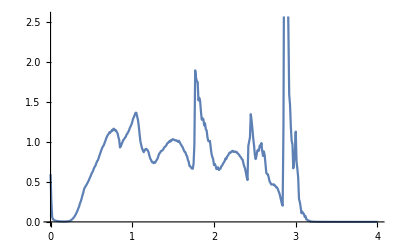

```mathematica
ListPlot[%47,Joined->True]
```

```mathematica
Import["10imp9.csv"]
```

{{0.,0.0390585},{0.01,0.0260842},{0.02,0.0192768},{0.03,0.0160527},{0.04,0.0126353},{0.05,0.0101487},{0.06,0.00889938},{0.07,0.00774857},{0.08,0.0066015},{0.09,0.00562472},{0.1,0.00482034},{0.11,0.00454071},{0.12,0.00414879},{0.13,0.00402491},{0.14,0.00377531},{0.15,0.00388357},{0.16,0.00404038},{0.17,0.00444706},{0.18,0.00486565},{0.19,0.00566206},{0.2,0.00675579},{0.21,0.00821216},{0.22,0.01095},{0.23,0.0153297},{0.24,0.018394},{0.25,0.0282455},{0.26,0.0443928},{0.27,0.0613392},{0.28,0.0832617},{0.29,0.106241},{0.3,0.133241},{0.31,0.161102},{0.32,0.19712},{0.33,0.22972},{0.34,0.271393},{0.35,0.306698},{0.36,0.341848},{0.37,0.37954},{0.38,0.41286},{0.39,0.43737},{0.4,0.458947},{0.41,0.474555},{0.42,0.482362},{0.43,0.501962},{0.44,0.529274},{0.45,0.551868},{0.46,0.578568},{0.47,0.610125},{0.48,0.637921},{0.49,0.670603},{0.5,0.699059},{0.51,0.732599},{0.52,0.763615},{0.53,0.798885},{0.54,0.828943},{0.55,0.868657},{0.56,0.895676},{0.57,0.928503},{0.58,0.962538},{0.59,0.99569},{0.6,1.02158},{0.61,1.05315},{0.62,1.08325},{0.63,1.10404},{0.64,1.13854},{0.65,1.15445},{0.66,1.18071},{0.67,1.19587},{0.68,1.21643},{0.69,1.22774},{0.7,1.24767},{0.71,1.26076},{0.72,1.26708},{0.73,1.2742},{0.74,1.27932},{0.75,1.28394},{0.76,1.28517},{0.77,1.28457},{0.78,1.27954},{0.79,1.27386},{0.8,1.26066},{0.81,1.24335},{0.82,1.22246},{0.83,1.17824},{0.84,1.10827},{0.85,0.994075},{0.86,1.03114},{0.87,1.06428},{0.88,1.09191},{0.89,1.11427},{0.9,1.13973},{0.91,1.16758},{0.92,1.20685},{0.93,1.22716},{0.94,1.26884},{0.95,1.29777},{0.96,1.32779},{0.97,1.37713},{0.98,1.41595},{0.99,1.45241},{1.,1.49456},{1.01,1.54027},{1.02,1.56977},{1.03,1.5883},{1.04,1.60881},{1.05,1.58268},{1.06,1.53336},{1.07,1.44028},{1.08,1.3049},{1.09,1.16393},{1.1,1.06287},{1.11,0.989913},{1.12,0.943471},{1.13,0.933407},{1.14,0.931666},{1.15,0.957326},{1.16,0.968392},{1.17,0.989767},{1.18,0.996193},{1.19,1.00105},{1.2,0.984798},{1.21,0.960745},{1.22,0.937642},{1.23,0.912829},{1.24,0.889824},{1.25,0.882287},{1.26,0.888978},{1.27,0.893512},{1.28,0.910752},{1.29,0.924523},{1.3,0.950721},{1.31,0.977013},{1.32,0.999894},{1.33,1.02185},{1.34,1.03679},{1.35,1.05242},{1.36,1.06972},{1.37,1.07528},{1.38,1.08763},{1.39,1.10515},{1.4,1.10491},{1.41,1.11371},{1.42,1.12679},{1.43,1.1436},{1.44,1.15886},{1.45,1.15462},{1.46,1.16864},{1.47,1.17205},{1.48,1.18437},{1.49,1.18113},{1.5,1.18304},{1.51,1.18378},{1.52,1.17933},{1.53,1.17353},{1.54,1.16634},{1.55,1.16157},{1.56,1.1584},{1.57,1.14643},{1.58,1.13634},{1.59,1.12393},{1.6,1.11143},{1.61,1.08743},{1.62,1.06652},{1.63,1.03948},{1.64,1.01899},{1.65,0.993811},{1.66,0.963644},{1.67,0.921648},{1.68,0.887948},{1.69,0.843807},{1.7,0.811234},{1.71,0.77568},{1.72,0.736746},{1.73,0.702703},{1.74,0.689755},{1.75,0.745941},{1.76,0.991557},{1.77,1.78466},{1.78,1.72917},{1.79,1.62256},{1.8,1.6389},{1.81,1.55735},{1.82,1.45968},{1.83,1.32698},{1.84,1.2593},{1.85,1.23591},{1.86,1.17879},{1.87,1.11861},{1.88,1.11183},{1.89,1.1029},{1.9,1.04524},{1.91,1.02013},{1.92,0.962922},{1.93,0.949691},{1.94,0.943841},{1.95,0.881587},{1.96,0.876801},{1.97,0.843812},{1.98,0.806227},{1.99,0.783559},{2.,0.759047},{2.01,0.750366},{2.02,0.744147},{2.03,0.748113},{2.04,0.752872},{2.05,0.768958},{2.06,0.774129},{2.07,0.786125},{2.08,0.794376},{2.09,0.818726},{2.1,0.839296},{2.11,0.852481},{2.12,0.859598},{2.13,0.874419},{2.14,0.897181},{2.15,0.898641},{2.16,0.904183},{2.17,0.931322},{2.18,0.933331},{2.19,0.940637},{2.2,0.93983},{2.21,0.940698},{2.22,0.947127},{2.23,0.937618},{2.24,0.937621},{2.25,0.928097},{2.26,0.92899},{2.27,0.914646},{2.28,0.906226},{2.29,0.90064},{2.3,0.890494},{2.31,0.872813},{2.32,0.85473},{2.33,0.835268},{2.34,0.814949},{2.35,0.783966},{2.36,0.757568},{2.37,0.715549},{2.38,0.670846},{2.39,0.616245},{2.4,0.542707},{2.41,0.555115},{2.42,1.22977},{2.43,1.14062},{2.44,1.10506},{2.45,1.00785},{2.46,0.934055},{2.47,0.837614},{2.48,0.877189},{2.49,0.799743},{2.5,0.821311},{2.51,0.848574},{2.52,0.860002},{2.53,0.863513},{2.54,0.877589},{2.55,0.840339},{2.56,0.848586},{2.57,0.870548},{2.58,0.88841},{2.59,0.849534},{2.6,0.822828},{2.61,0.850878},{2.62,0.823729},{2.63,0.740393},{2.64,0.690241},{2.65,0.64487},{2.66,0.590714},{2.67,0.540301},{2.68,0.523878},{2.69,0.502761},{2.7,0.493697},{2.71,0.482331},{2.72,0.477163},{2.73,0.471699},{2.74,0.462393},{2.75,0.452358},{2.76,0.433869},{2.77,0.422186},{2.78,0.40099},{2.79,0.38317},{2.8,0.361896},{2.81,0.340012},{2.82,0.32363},{2.83,0.316573},{2.84,0.374622},{2.85,3.63243},{2.86,6.03126},{2.87,3.99761},{2.88,3.35762},{2.89,2.4762},{2.9,1.55986},{2.91,1.1466},{2.92,1.14389},{2.93,1.1273},{2.94,1.21904},{2.95,1.09657},{2.96,1.09458},{2.97,0.999718},{2.98,0.959598},{2.99,0.969299},{3.,0.783045},{3.01,0.558651},{3.02,0.569639},{3.03,0.512283},{3.04,0.359397},{3.05,0.408913},{3.06,0.297225},{3.07,0.217205},{3.08,0.19621},{3.09,0.136755},{3.1,0.0753411},{3.11,0.064565},{3.12,0.042641},{3.13,0.0337406},{3.14,0.0131793},{3.15,0.0160114},{3.16,0.00816432},{3.17,0.00697072},{3.18,0.00330477},{3.19,0.00284523},{3.2,0.00210139},{3.21,0.00197816},{3.22,0.00149558},{3.23,0.00129571},{3.24,0.00113275},{3.25,0.00105511},{3.26,0.000938633},{3.27,0.000830511},{3.28,0.000774901},{3.29,0.000693972},{3.3,0.000638083},{3.31,0.000577369},{3.32,0.000527818},{3.33,0.000486802},{3.34,0.000443572},{3.35,0.000405418},{3.36,0.000382036},{3.37,0.000345661},{3.38,0.000324093},{3.39,0.000303631},{3.4,0.000284422},{3.41,0.000257442},{3.42,0.00024304},{3.43,0.000225493},{3.44,0.000209461},{3.45,0.000197799},{3.46,0.000184661},{3.47,0.000170103},{3.48,0.000158971},{3.49,0.000150368},{3.5,0.000140306},{3.51,0.000132073},{3.52,0.000123561},{3.53,0.000118569},{3.54,0.000110368},{3.55,0.000103976},{3.56,0.0000998354},{3.57,0.0000924478},{3.58,0.0000860321},{3.59,0.0000828422},{3.6,0.0000773154},{3.61,0.0000730871},{3.62,0.0000694484},{3.63,0.000065375},{3.64,0.0000625748},{3.65,0.0000600303},{3.66,0.0000563325},{3.67,0.0000530122},{3.68,0.0000504352},{3.69,0.0000476461},{3.7,0.0000443833},{3.71,0.0000429536},{3.72,0.0000411302},{3.73,0.0000392733},{3.74,0.0000369062},{3.75,0.0000353093},{3.76,0.0000332811},{3.77,0.0000316047},{3.78,0.0000307862},{3.79,0.0000290516},{3.8,0.0000275744},{3.81,0.000026008},{3.82,0.0000251241},{3.83,0.000024099},{3.84,0.000023585},{3.85,0.0000217798},{3.86,0.0000208199},{3.87,0.0000202034},{3.88,0.0000192007},{3.89,0.0000183581},{3.9,0.0000173493},{3.91,0.0000168252},{3.92,0.0000159032},{3.93,0.0000153266},{3.94,0.000015053},{3.95,0.0000141565},{3.96,0.0000134342},{3.97,0.0000128735},{3.98,0.0000124871},{3.99,0.0000119054},{4.,0.0000115272}}

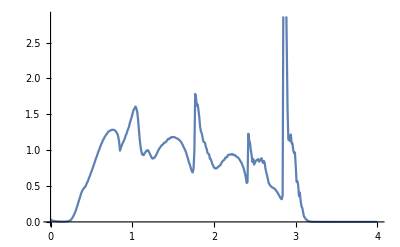

```mathematica
ListPlot[%2,Joined->True]
```